# ME314 - Final Project Gerik Zatorski

```mathematica
Quit[];
```

```mathematica
(* INITIALIZATION CELL *)

(* SE(2) representation of rigid body motion in the plane *)
g[x_,y_,θ_]={{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}};
(* unhat takes a 3x3 matrix that is assumed to be ginv.gdot for SE(2) and returns a 3x1 vector. The first two components are the linear velocities in x and y and the third component is the angular velocity (around the "z" axis that is out of the plane of motion *)
unhat[a_]:={a[[1,3]],a[[2,3]],a[[2,1]]};
(* hat[] takes a 3x1 vector and creates a 3x3 matrix *)
hat[a_]:={{0,-a[[3]],a[[1]]},{a[[3]],0,a[[2]]},{0,0,0}};
(* Hom[] takes a point in the plane and adds a 1 to the end of it to create a homogeneous representation of that point. This is used for animation *)
Hom[pt_]:=Flatten[{pt,1}];
(* UnHom[] takes a homogeneous representation of a point and returns the point in the plane by removing the 1 at the end *)
UnHom[pt_]:={pt[[1]],pt[[2]]};
(* Distance between two points in 2D plane *)
Distance2D[x_,y_]:=Sqrt[(x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2];

(* Conversions *)
FtToM=0.3048;

(* Ball Constants *)
m=0.625;
diameterBall=9.55/12*FtToM;
rball=diameterBall/2;
```

## Phase 1 (hold -> roll)

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1}.

1.25664

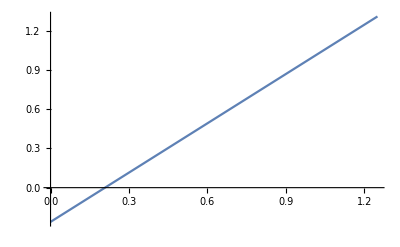

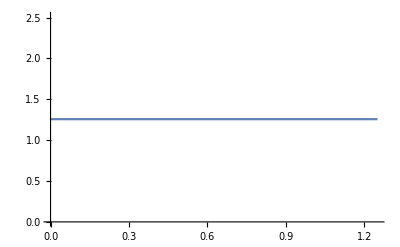

```mathematica
(* link dimensions *)
L1=1;

(* Joint Frame Transformations *)
g0=g[0,0,θ0[t]];
ghand=g0.g[L1/2,0,0];
g2=g0.g[L1,0,θ2[t]];

(* Ball Frame Transformations *)
gballbefore=g0.g[L1/2,rball,0]; (* transformation before ball is released from constraint *)
gline1before=gballbefore.g[-rball,0,0];
gline2before=gballbefore.g[rball,0,0];

(* Fake Joint Positions *)
tMax=5/4;
θ0sol=ListInterpolation[Pi/12*{-1,5},{0,tMax}][t];

(* Fake Joint Velocities and Accelerations *)
θ0dotsol = D[θ0sol,t];
θ0dotdotsol = D[θ0dotsol,t];

(* Joint Coordinates *)
coordj0[time_]:=({g0[[1,3]],g0[[2,3]]}/.{θ0[t]->θ0sol,θ2[t]->θ2sol})/.t->time;
coordj2[time_]:=({g2[[1,3]],g2[[2,3]]}/.{θ0[t]->θ0sol,θ2[t]->θ2sol})/.t->time;

(* Ball Coordinates *)
coordballbefore[time_]:=({gballbefore[[1,3]],gballbefore[[2,3]]}/.{θ0[t]->θ0sol,θ2[t]->θ2sol})/.t->time;
coordline1before[time_]:=({gline1before[[1,3]],gline1before[[2,3]]}/.{θ0[t]->θ0sol,θ2[t]->θ2sol})/.t->time;
coordline2before[time_]:=({gline2before[[1,3]],gline2before[[2,3]]}/.{θ0[t]->θ0sol,θ2[t]->θ2sol})/.t->time;

(* Link Graphics *)
GraphicsL1=Line[{coordj0[t],coordj2[t]}];

(* Ball Graphics *)
Graphicsballbefore = Circle[coordballbefore[t],rball];
Graphicsballlinebefore=Line[{coordline1before[t],coordline2before[t]}];

(* Solving for conditions at roll *)
troll=0.05;
tr=gballbefore/.{θ0[t]->θ0sol};
xr=tr[[1,3]]/.t->troll;
yr=tr[[2,3]]/.t->troll;
θr=θ0[t]/.{θ0[t]->θ0sol}/.t->troll;

(* dot sol exact *)
θrdot=θ0dotsol/.t->troll
trdot=D[gballbefore,t]/.{θ0[t]->θ0sol,θ0'[t]->θ0dotsol};
xrdot=trdot[[1,3]]/.t->troll;
yrdot=trdot[[2,3]]/.t->troll;

(* Plots *)
Plot[θ0sol,{t,0,tMax}]
Plot[θ0dotsol,{t,0,tMax}]

(* Animations *)
Animate[
Show[
Graphics[{
Black,GraphicsL1/.t->time,
Black,Graphicsballbefore/.t->time,
Black,Graphicsballlinebefore/.t->time
},Axes->True]
],
{time,0,tMax},
AnimationRunning->False,
AnimationRate->1.0
]
```

## Phase 2 (roll -> release)

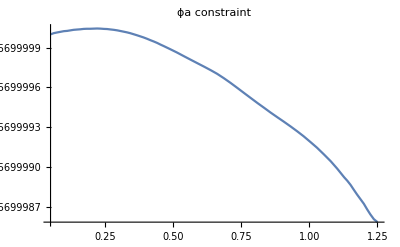

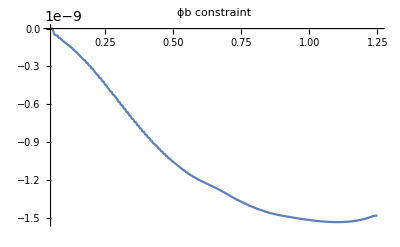

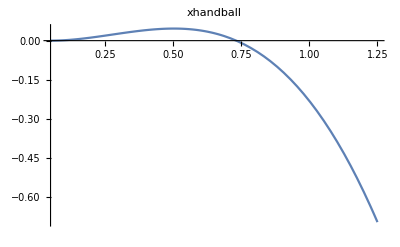

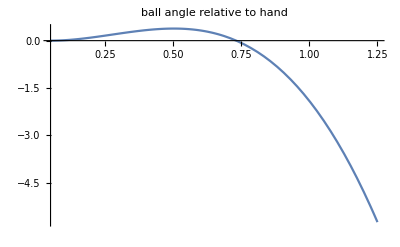

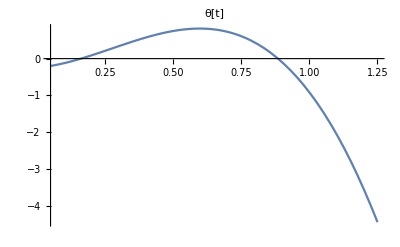

```mathematica
(* New Ball Frame Transforms for time after roll *)
gball=g[x[t],y[t],θ[t]];
ghandball=Inverse[ghand].gball; (* ball in hand frame *)
θhandball=θ[t]-θ0[t];
xhandball=ghandball[[1,3]];
gcontact=g0.g[L1/2-rball*θhandball,0,0];
 
(* Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* Lagrangian using body velocities (see lecture 23) *)
Vball=unhat[Inverse[gball].D[gball,t]];
Iball=DiagonalMatrix[{m,m,J}];
J=m*rball^2;
KE=1/2*(Vball.Iball).{Vball}ᵀ;
PE=m*grav*y[t];
Lag =KE-PE;

(***************************************************************************)
(* Constraints and External forces *)
(***************************************************************************)

(* Point of contact *)
mhand=(g2[[2,3]]-g0[[2,3]])/(g2[[1,3]]-g0[[1,3]]);
Eqhand=contacty-g2[[2,3]]==mhand*(contactx-g2[[1,3]]);
Eqprojection=contacty-gball[[2,3]]==-1/mhand*(contactx-gball[[1,3]]);
contacttemp=Solve[{Eqhand&&Eqprojection},{contactx,contacty}];
contactx=contacttemp[[1,1,2]];
contacty=contacttemp[[1,2,2]];

(* Constraints *)
(* Ball remains in contact with last link *)
ϕa=ghandball[[2,3]]+rball;

(* Ball rolls without slipping where x=rball*θ *)
ϕb=xhandball-rball*θhandball;

(* gotta do this *)
θ0[t]=θ0sol;
θ0'[t]=θ0dotsol;
θ0''[t]=θ0dotdotsol;

(***************************************************************************)
(* Euler-Lagrange equations VECTORS *)
(***************************************************************************)

(* Using BOTH Constraints *)
Eq1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]==λa*D[ϕa,x[t]]+λb*D[ϕb,x[t]];
Eq2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]==λa*D[ϕa,y[t]]+λb*D[ϕb,y[t]];
Eq3=D[D[Lag,θ'[t]],t]-D[Lag,θ[t]]==λa*D[ϕa,θ[t]]+λb*D[ϕb,θ[t]];
Eq4=D[D[ϕa,t],t]==0;
Eq5=D[D[ϕb,t],t]==0;
ELtemp=Solve[{Eq1&&Eq2&&Eq3&&Eq4&&Eq5},{x''[t],y''[t],θ''[t],λa,λb}];

EL={x''[t]==ELtemp[[1,1,2]],y''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Constants and Initial Condition *)
grav = 9.8;
InitCon={x[troll]==xr,y[troll]==yr,θ[troll]==θr,x'[troll]==xrdot,y'[troll]==yrdot,θ'[troll]==θrdot};

(***************************************************************************)
(* Numerical Solutions *)
(***************************************************************************)

J0=θ0sol/.t->time;
tRelease=0;
sol=NDSolve[Join[EL,InitCon,
(* determine time of release *)
{WhenEvent[rball*(θ[t]-J0/.time->t)>L1/2,
{Print["Let it fly!"],tRelease=t,Print[tRelease],"StopIntegration"},
"DetectionMethod"->"Sign"]}
],{x,y,θ},{t,troll,tMax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4}];

xsol=x[t]/.sol;
ysol=y[t]/.sol;
θsol=θ[t]/.sol;

(***************************************************************************)
(* PLOTS AND ANIMATION *)
(***************************************************************************)

Plot[ϕa/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tMax},PlotLabel->"ϕa constraint"]
Plot[ϕb/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tMax},PlotLabel->"ϕb constraint"]
Plot[(xhandball)/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tMax},PlotLabel->"xhandball"]
Plot[θhandball/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tMax},PlotLabel->"ball angle relative to hand"]
Plot[θ[t]/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tMax},PlotLabel->"θ[t]"]

(*
Plot[ghandball[[2,3]]/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tMax}]
Plot[(gcontact[[1,3]])/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tMax}]*)

(* Dynamic ball coords and graphics *)
coordball[time_]:=({gball[[1,3]],gball[[2,3]]}/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
gmidline1=gball.g[-rball,0,0];
gmidline2=gball.g[rball,0,0];
coordmidline1[time_]:=({gmidline1[[1,3]],gmidline1[[2,3]]}/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordmidline2[time_]:=({gmidline2[[1,3]],gmidline2[[2,3]]}/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;

Graphicsball = Circle[{coordball[t][[1]][[1]],coordball[t][[2]][[1]]},rball];
Graphicsballline=Line[{{coordmidline1[t][[1]][[1]],coordmidline1[t][[2]][[1]]},{coordmidline2[t][[1]][[1]],coordmidline2[t][[2]][[1]]}}];

coordcontact[time_]:=({contactx,contacty}/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
Graphicscontact=Locator[{coordcontact[t][[1]][[1]],coordcontact[t][[2]][[1]]}];

Animate[
Show[
Graphics[{
Black,GraphicsL1/.t->time,
Black,Graphicsball/.t->time,
Black,Graphicsballline/.t->time,
Graphicscontact/.t->time
}],
(*PlotRange->{{-1,8},{-1,8}},*)
Axes->True
],
{time,troll,tMax},
AnimationRunning->False,
AnimationRate->1.0
]
```